# Graphs for ML course

## Activation functions

The following cells will be used one only for the installation. It was based on Linux.

```mathematica
Needs["PacletManager`"]
PacletInstall["~/Downloads/MaTeX-1.7.10.paclet"]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

Click here for documentation on configuring MaTeX.

```mathematica
ConfigureMaTeX["pdfLaTeX"-> "/opt/software/texlive/2024/bin/x86_64-linux/pdflatex","Ghostscript"-> "/usr/bin/gs"]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→/opt/software/texlive/2024/bin/x86_64-linux/pdflatex,Ghostscript→/usr/bin/gs}

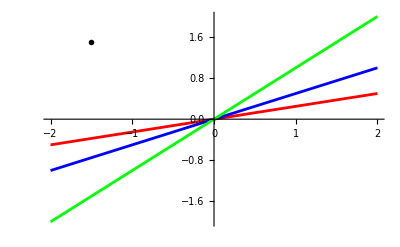

```mathematica
Plot[{.25x,0.5x,x},{x,-2,2},PlotStyle->{Red,Blue, Green},
Epilog->{Inset[MaTeX["f(x)=kx",Magnification->2],{-1.5,1.5},Scaled[{0.5,1}]]}]
```

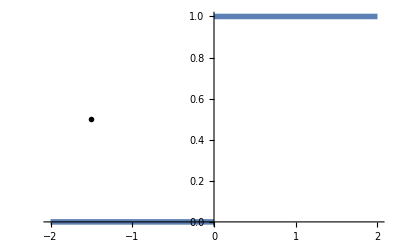

```mathematica
Plot[Piecewise[{{0,x<0},{1,x>0}}],{x,-2,2},PlotStyle->{Thickness[0.01]},
Epilog->{Inset[MaTeX["H(x)",Magnification->2],{-1.5,.5},Scaled[{0.5,1}]]}]
```

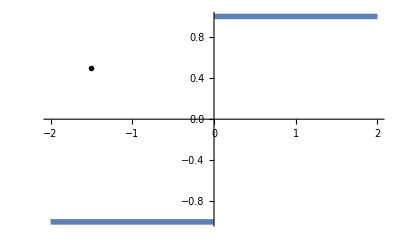

```mathematica
Plot[Piecewise[{{-1,x<0},{1,x>0}}],{x,-2,2},
PlotStyle->{Thickness[0.01]},
Epilog->{Inset[MaTeX["S(x)",Magnification->2],{-1.5,.5},Scaled[{0.5,1}]]}]
```

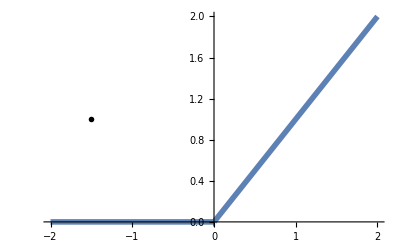

```mathematica
Plot[Piecewise[{{0,x<0},{x,x>0}}],{x,-2,2},
PlotStyle->{Thickness[0.01]},
Epilog->{Inset[MaTeX["Relu(x)",Magnification->2],{-1.5,1},Scaled[{0.5,1}]]}]
```

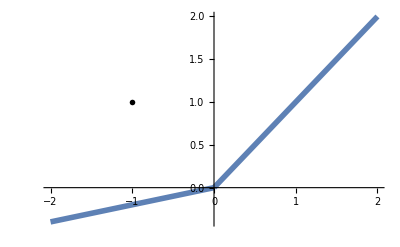

```mathematica
Plot[Piecewise[{{.2x,x<0},{x,x>0}}],{x,-2,2},
PlotStyle->{Thickness[0.01]},
Epilog->{Inset[MaTeX["PRelu(\\alpha x)",Magnification->2],{-1,1},Scaled[{0.5,1}]]}]
```

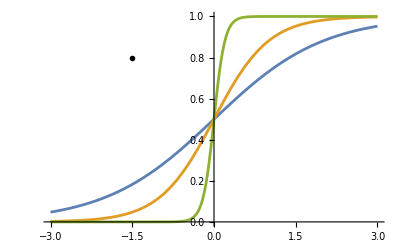

```mathematica
Plot[{LogisticSigmoid[x],LogisticSigmoid[2x],LogisticSigmoid[10x]},{x,-3,3},
Epilog->{Inset[MaTeX["\\sigma_c(x)",Magnification->2],{-1.5,0.8},Scaled[{0.5,1}]]}]
```

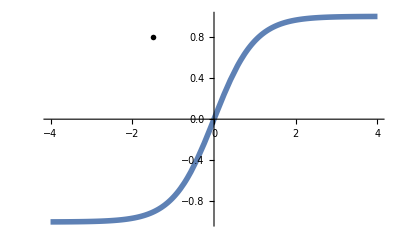

```mathematica
Plot[Tanh[x],{x,-4,4},PlotStyle->{Thickness[0.01]},
Epilog->{Inset[MaTeX["\\tanh (x)",Magnification->2],{-1.5,0.8},Scaled[{0.5,1}]]}]
```

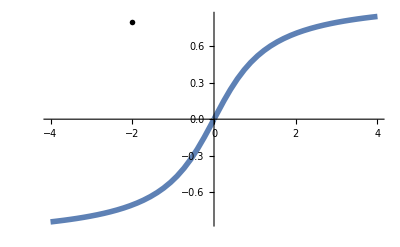

```mathematica
Plot[(2ArcTan[x])/Pi,{x,-4,4},PlotStyle->{Thickness[0.01]},
Epilog->{Inset[MaTeX["(2/\\pi)\\arctan (x)",Magnification->2],{-2,0.8},Scaled[{0.5,1}]]}]
```

## Cross-entropy calculations

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
PDF[NormalDistribution[0,5],x]
```

(ⅇ^(-x^2/50))/(5 √(2 π))

```mathematica
-Integrate[PDF[NormalDistribution[0,5],x]*Log[PDF[NormalDistribution[0,1],x]],{x,-100,100}]//N
```

13.4189

```mathematica
-Integrate[PDF[NormalDistribution[0,1],x]*Log[PDF[NormalDistribution[0,5],x]],{x,-50,50}]//N
```

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

2.54838

Shannon entropy

```mathematica
-Integrate[PDF[NormalDistribution[0,1],x]*Log[PDF[NormalDistribution[0,1],x]],{x,-50,50}]//N
```

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

1.41894

```mathematica
-Integrate[PDF[NormalDistribution[0,5],x]*Log[PDF[NormalDistribution[0,5],x]],{x,-50,50}]//N
```

3.02838